```mathematica
Collect[(6 (z[p]/(c β+d)+m β+n)^2+6(1-(a β+b)/(c β+d))(z[p]/(c β+d)+m β+n)+((a β+b)/(c β+d))^2-3(a β+b)/(c β+d)+1)/(24 β),z[p]]
```

(1+6 n^2+12 m n β+6 m^2 β^2+(b+a β)^2/(d+c β)^2-(3 (b+a β))/(d+c β)+6 n (1-(b+a β)/(d+c β))+6 m β (1-(b+a β)/(d+c β)))/(24 β)+(((12 n)/(d+c β)+(12 m β)/(d+c β)+(6 (1-(b+a β)/(d+c β)))/(d+c β)) z[p])/(24 β)+z[p]^2/(4 β (d+c β)^2)

```mathematica
FullSimplify[(1+6 n^2+12 m n β+6 m^2 β^2+(b+a β)^2/(d+c β)^2-(3 (b+a β))/(d+c β)+6 n (1-(b+a β)/(d+c β))+6 m β (1-(b+a β)/(d+c β)))/(24 β)]
```

(1+6 n+6 n^2+6 m β+12 m n β+6 m^2 β^2+(b+a β)^2/(d+c β)^2-(3 (b+a β))/(d+c β)-(6 n (b+a β))/(d+c β)-(6 m β (b+a β))/(d+c β))/(24 β)

```mathematica
(1/t(Sinh[(Q/2-w)t]/(2Sinh[b1 t/2]Sinh[b2 t/2])-(Q-2w)/(b1 b2 t))/.Q->b1+b2)//TrigToExp//FullSimplify
```

```mathematica
(ⅇ^(-t w)-ⅇ^(-t (b1+b2-w)))/((1-ⅇ^(-b1 t)) (1-ⅇ^(-b2 t)) t)-(b1+b2-2w)/(b1 b2 t^2)/.t->(t+1)/2
```

Integrate this from -1 to 1 with GaussLegendre quadrature.

```mathematica
(-ⅇ^(-1/2 (1+t) (b1+b2-w))+ⅇ^(-1/2 (1+t) w))/((1-ⅇ^(-1/2 b1 (1+t))) (1-ⅇ^(-1/2 b2 (1+t))) (1+t))-(2(b1+b2-2 w))/(b1 b2 (1+t)^2)
```

Add the boundary term as before.
Then integrate these from 0 to ∞ with GaussLaguerre quadrature.

```mathematica
ⅇ^-t ⅇ^(b1+b2-w)/((ⅇ^b1-ⅇ^(-b1 t/w)) (ⅇ^b2-ⅇ^(-b2 t/w)) (w+t))
-ⅇ^-t ⅇ^w/((ⅇ^b1-ⅇ^(-b1 t/(b1+b2-w))) (ⅇ^b2-ⅇ^(-b2 t/(b1+b2-w))) (b1+b2-w+t))
```

```mathematica
ⅇ^-t(ⅇ^(b1+b2-w)/((ⅇ^b1-ⅇ^(-b1 t/w)) (ⅇ^b2-ⅇ^(-b2 t/w)) (w+t))-ⅇ^w/((ⅇ^b1-ⅇ^(-b1 t/(b1+b2-w))) (ⅇ^b2-ⅇ^(-b2 t/(b1+b2-w))) (b1+b2-w+t)))
```

```mathematica
g0[w_,b1_,b2_,t_]:=ⅇ^-w/((1-ⅇ^(-b1 (t/w+1))) (1-ⅇ^(-b2 (t/w+1))) w (t/w+1))
g[w_,b1_,b2_,t_]:=g0[w,b1,b2,t]-g0[b1+b2-w,b1,b2,t]
```

ⅇ^-x/x

```mathematica
ⅇ^-t g[w,b1,b2,t]
```

ⅇ^-t (-ⅇ^(-b1-b2+w)/((1-ⅇ^(-b1 (1+t/(b1+b2-w)))) (1-ⅇ^(-b2 (1+t/(b1+b2-w)))) (1+t/(b1+b2-w)) (b1+b2-w))+ⅇ^-w/((1-ⅇ^(-b1 (1+t/w))) (1-ⅇ^(-b2 (1+t/w))) (1+t/w) w))

```mathematica
FullSimplify[(ⅇ^-w (-b1 ⅇ^(b1+b2+(b1 t)/w+(b2 t)/w)-b2 ⅇ^(b1+b2+(b1 t)/w+(b2 t)/w)+b1 ⅇ^(2 b1+b2+(b1 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w)+b2 ⅇ^(2 b1+b2+(b1 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w)+b1 ⅇ^(b1+2 b2+(b2 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w)+b2 ⅇ^(b1+2 b2+(b2 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w)-b1 ⅇ^(2 b1+2 b2+(b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w)-b2 ⅇ^(2 b1+2 b2+(b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w)-ⅇ^(b1+b2+(b1 t)/w+(b2 t)/w) t+ⅇ^(2 b1+b2+(b1 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w) t+ⅇ^(b1+2 b2+(b2 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w) t-ⅇ^(2 b1+2 b2+(b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w) t+ⅇ^((b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+2 w) t-ⅇ^(b1+(b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+(b1 t)/w+2 w) t-ⅇ^(b2+(b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+(b2 t)/w+2 w) t+ⅇ^(b1+b2+(b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w+2 w) t+ⅇ^(b1+b2+(b1 t)/w+(b2 t)/w) w-ⅇ^(2 b1+b2+(b1 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w) w-ⅇ^(b1+2 b2+(b2 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w) w+ⅇ^(2 b1+2 b2+(b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w) w+ⅇ^((b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+2 w) w-ⅇ^(b1+(b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+(b1 t)/w+2 w) w-ⅇ^(b2+(b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+(b2 t)/w+2 w) w+ⅇ^(b1+b2+(b1 t)/(b1+b2-w)+(b2 t)/(b1+b2-w)+(b1 t)/w+(b2 t)/w+2 w) w))/((-1+ⅇ^(b1+(b1 t)/(b1+b2-w))) (-1+ⅇ^(b2+(b2 t)/(b1+b2-w))) (-1+ⅇ^(b1+(b1 t)/w)) (-1+ⅇ^(b2+(b2 t)/w)) (-b1-b2-t+w) (t+w)),t>0∧b1>0∧b2>0∧b1+b2>w>0]
```

$Aborted

```mathematica
z=t w
dz=w dt
t=z/w
dt = dz/w
t=0 -> z=0
t=∞->z=∞
```

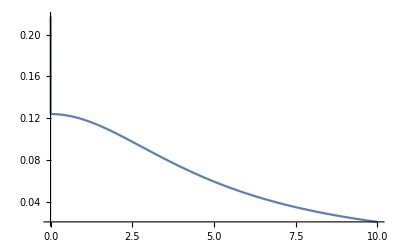

```mathematica
Plot[-(4/5+√2)/(√2 t^2)+(ⅇ^(-t/10)-ⅇ^(-(9/10+√2) t))/((1-ⅇ^-t) (1-ⅇ^(-√2 t)) t),{t,0,10}]
```

```mathematica
-(4/5+b)/(b t^2)+(ⅇ^(-t/10)-ⅇ^(-(9/10+b) t))/((1-ⅇ^-t) (1-ⅇ^(-b t)) t)
```

```mathematica
ⅇ^(-t w)((1-ⅇ^(-t (b1+b2-2w)))/((1-ⅇ^(-b1 t)) (1-ⅇ^(-b2 t)) t)-ⅇ^(t w)(b1+b2-2w)/(b1 b2 t^2))
```

```mathematica
(ⅇ^(-t w)-ⅇ^(-t (b1+b2-w)))/((1-ⅇ^(-b1 t)) (1-ⅇ^(-b2 t)) t)-(b1+b2-2w)/(b1 b2 t^2)
```

```mathematica
(w/(b1 b2 t^2)+ⅇ^(-t w)/((1-ⅇ^(-b1 t)) (1-ⅇ^(-b2 t)) t))-(ⅇ^(-t (b1+b2-w))/((1-ⅇ^(-b1 t)) (1-ⅇ^(-b2 t)) t)+(b1+b2-w)/(b1 b2 t^2))
```

```mathematica
(ⅇ^(-t w)-ⅇ^(-t (b1+b2-w)))/((1-ⅇ^(-b1 t)) (1-ⅇ^(-b2 t)) t)-(b1+b2-2w)/(b1 b2 t^2)/.{b1->b,b2->1,w->1/2,t->1.4457892618017823 10^-5}
```

-4.78399×10^9+(4.78402×10^9 (0.999993-ⅇ^(-0.0000144579 (1/2+b))))/(1-ⅇ^(-0.0000144579 b))

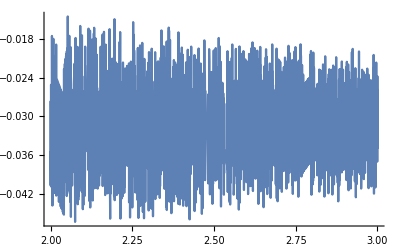

```mathematica
Plot[-4.783987215097575*^9+(4.784021798377713*^9 (0.9999927710798198-ⅇ^(-0.000014457892618017824 (1/2+b))))/(1-ⅇ^(-0.000014457892618017824 b)),{b,2,3}]
```

```mathematica
(4.784021798377713*^9 (-ⅇ^(-0.000014457892618017824 (1+b-w))+ⅇ^(-0.000014457892618017824 w)))/(1-ⅇ^(-0.000014457892618017824 b))-(4.783987215097575*^9 (1+b-2 w))/b
```

```mathematica
Series[(ⅇ^(-t w)-ⅇ^(-t (b1+b2-w)))/((1-ⅇ^(-b1 t)) (1-ⅇ^(-b2 t)) t)-(b1+b2-2w)/(b1 b2 t^2),{t,0,3}]//FullSimplify
```

((b1+b2-2 w) (b1 b2-2 (b1+b2) w+2 w^2))/(12 b1 b2)+1/(720 b1 b2)(-b1 b2 (b1^3+b2^3)+2 (b1^4-5 b1^2 b2^2+b2^4) w+30 b1 b2 (b1+b2) w^2-20 (b1^2+3 b1 b2+b2^2) w^3+30 (b1+b2) w^4-12 w^5) t^2+O[t]^4

```mathematica
(ⅇ^(-t w)-ⅇ^(-t (b1+b2-w)))/((1-ⅇ^(-b1 t)) (1-ⅇ^(-b2 t)) t)-(b1+b2-2 w)/(b1 b2 t^2)
```

```mathematica
t (b1+b2-2 w)+t w//Expand
```

b1 t+b2 t-t w

```mathematica
(ⅇ^(1/2 t (b1+b2-Q+2 w)) (-1+ⅇ^(t (Q-2 w))))/((-1+ⅇ^(b1 t)) (-1+ⅇ^(b2 t))t)-(Q-2 w)/(b1 b2 t^2)
```

```mathematica
Series[Exp[-t w]/(t (1-Exp[-b1 t])(1-Exp[-b2 t]))-Exp[-t (b1+b2-w)]/(t (1-Exp[-b1 t])(1-Exp[-b2 t]))-(b1+b2-2 w)/(b1 b2 t^2)
```

```mathematica
f[t]=Sinh[((b1+b2)/2-w)*t]/(2*t*Sinh[b1*t/2]*Sinh[b2*t/2])-(b1+b2-2*w)/(b1*b2*t^2)
```

-(b1+b2-2 w)/(b1 b2 t^2)+(Csch[(b1 t)/2] Csch[(b2 t)/2] Sinh[t ((b1+b2)/2-w)])/(2 t)

```mathematica
Simplify[t/(1!) Limit[f[t],t->0,Direction->"FromAbove"],b1>0∧b2>0∧b1+b2>w>0]
Simplify[t^3/(3!)Limit[D[f[t],t,t],t->0,Direction->"FromAbove"],b1>0∧b2>0∧b1+b2>w>0]
Simplify[t^5/(5!) Limit[D[f[t],t,t,t,t],t->0,Direction->"FromAbove"],b1>0∧b2>0∧b1+b2>w>0]
```

(t (b1+b2-2 w) (b1 (b2-2 w)+2 w (-b2+w)))/(12 b1 b2)

-1/(2160 b1 b2)t^3 (b1+b2-2 w) (b1^3 (b2-2 w)-b1^2 (b2-2 w)^2-2 w (b2^3+2 b2^2 w-6 b2 w^2+3 w^3)+b1 (b2^3+4 b2^2 w-18 b2 w^2+12 w^3))

1/(151200 b1 b2)t^5 (b1+b2-2 w) (b1^5 (b2-2 w)-b1^4 (b2-2 w)^2-b1^2 (b2-2 w)^2 (b2^2+3 b2 w-3 w^2)+b1 (b2-2 w) (b2^2+3 b2 w-3 w^2)^2+b1^3 (b2^3+b2^2 w-9 b2 w^2+6 w^3)+2 w (-b2^5-2 b2^4 w+3 b2^3 w^2+6 b2^2 w^3-9 b2 w^4+3 w^5))

```mathematica
Simplify[-1/(2160 b1 b2)t^3 (b1+b2-2 w) (b1^3 (b2-2 w)-b1^2 (b2-2 w)^2-2 w (b2^3+2 b2^2 w-6 b2 w^2+3 w^3)+b1 (b2^3+4 b2^2 w-18 b2 w^2+12 w^3))/.{b1->b,b2->b},b>0∧1+b>w>0]
```

-(t^3 (b-w) (b^4+4 b^3 w-26 b^2 w^2+24 b w^3-6 w^4))/(1080 b^2)

```mathematica
-(t^3 (b-w) (b^4+4 b^3 w-26 b^2 w^2+24 b w^3-6 w^4))/(1080 b^2)
```

```mathematica
-(t^3 (b-w) (b^4+4 b^3 w-26 b^2 w^2+24 b w^3-6 w^4))/(1080 b^2)/.t->ϵ b
```

-(b (b-w) (b^4+4 b^3 w-26 b^2 w^2+24 b w^3-6 w^4) ϵ^3)/1080

```mathematica
D[-(b (b-w) (b^4+4 b^3 w-26 b^2 w^2+24 b w^3-6 w^4))/1080,w]//Simplify
```

```mathematica
Simplify[Solve[(b^4-20 b^3 w+50 b^2 w^2-40 b w^3+10 w^4)==0,w],1+b>w>0∧b>0]
```

{{w→b-√(1/10 (5-√15)) b},{w→(1+√(1/10 (5-√15))) b},{w→b-√(1/10 (5+√15)) b},{w→(1+√(1/10 (5+√15))) b}}

```mathematica
Simplify[-(t^3 (b-w) (b^4+4 b^3 w-26 b^2 w^2+24 b w^3-6 w^4))/(1080 b^2)/.{{w->b-√(1/10 (5-√15)) b},{w->(1+√(1/10 (5-√15))) b},{w->b-√(1/10 (5+√15)) b},{w->(1+√(1/10 (5+√15))) b}},1+b>w>0∧b>0]/.t->ϵ b
```

{(√(1/10 (5-√15)) (1+√15) b^6 ϵ^3)/2700,-(√(1/10 (5-√15)) (1+√15) b^6 ϵ^3)/2700,-((-1+√15) √(1/10 (5+√15)) b^6 ϵ^3)/2700,((-1+√15) √(1/10 (5+√15)) b^6 ϵ^3)/2700}

```mathematica
{(√(1/10 (5-√15)) (1+√15) b^6 ϵ^3)/2700,-(√(1/10 (5-√15)) (1+√15) b^6 ϵ^3)/2700,-((-1+√15) √(1/10 (5+√15)) b^6 ϵ^3)/2700,((-1+√15) √(1/10 (5+√15)) b^6 ϵ^3)/2700}/(b^6 ϵ^3)
```

```mathematica
{(√(1/10 (5-√15)) (1+√15))/2700,-(√(1/10 (5-√15)) (1+√15))/2700,-((-1+√15) √(1/10 (5+√15)))/2700,((-1+√15) √(1/10 (5+√15)))/2700}//N
```

{0.000605894,-0.000605894,-0.00100231,0.00100231}

```mathematica
0.0010025*b^3 t^3
```